```mathematica
Clear["Global`*"]
```

```mathematica
(* Functions to form Butcher matrices/vectors given coefficients. S# stands for #-order SDIRK, where the diagonal entry is given first in the parameters, and D# stands for #-order DIRK. *)
S1[ad_]:={{ad}};
S2[ad_,a21_] :={{ad,0},{a21,ad}};
D2[a11_,a21_,a22_] :={{a11,0},{a21,a22}};
S3[ad_,a21_,a31_,a32_] :={{ad,0,0},{a21,ad,0},{a31,a32,ad}};
D3[a11_,a21_,a22_,a31_,a32_,a33_] :={{a11,0,0},{a21,a22,0},{a31,a32,a33}};
S4[ad_,a21_,a31_,a32_,a41_,a42_,a43_] :={{ad,0,0,0},{a21,ad,0,0},{a31,a32,ad,0},{a41,a42,a43,ad}};
D4[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_] :={{a11,0,0,0},{a21,a22,0,0},{a31,a32,a33,0},{a41,a42,a43,a44}};
S5[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{ad,0,0,0,0},{a21,ad,0,0,0},{a31,a32,ad,0,0},{a41,a42,a43,ad,0},{a51,a52,a53,a54,ad}};
D5[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_] :={{a11,0,0,0,0},{a21,a22,0,0,0},{a31,a32,a33,0,0},{a41,a42,a43,a44,0},{a51,a52,a53,a54,a55}};
S6[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{ad,0,0,0,0,0},{a21,ad,0,0,0,0},{a31,a32,ad,0,0,0},{a41,a42,a43,ad,0,0},{a51,a52,a53,a54,ad,0},{a61,a62,a63,a64,a65,ad}};
D6[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_,a61_,a62_,a63_,a64_,a65_,a66_] :={{a11,0,0,0,0,0},{a21,a22,0,0,0,0},{a31,a32,a33,0,0,0},{a41,a42,a43,a44,0,0},{a51,a52,a53,a54,a55,0},{a61,a62,a63,a64,a65,a66}};
E1:={{0.0}};
E2[a21_] :={{0,0},{a21,0}};
E3[a21_,a31_,a32_] :={{0,0,0},{a21,0,0},{a31,a32,0}};
E4[a21_,a31_,a32_,a41_,a42_,a43_] :={{0,0,0,0},{a21,0,0,0},{a31,a32,0,0},{a41,a42,a43,0}};
E5[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{0,0,0,0,0},{a21,0,0,0,0},{a31,a32,0,0,0},{a41,a42,a43,0,0},{a51,a52,a53,a54,0}};
E6[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{0,0,0,0,0,0},{a21,0,0,0,0,0},{a31,a32,0,0,0,0},{a41,a42,a43,0,0,0},{a51,a52,a53,a54,0,0},{a61,a62,a63,a64,a65,0}};
b1[bb1_]:={{bb1}};
b2[bb1_,bb2_]:={{bb1,bb2}};
b3[bb1_,bb2_,bb3_]:={{bb1,bb2,bb3}};
b4[bb1_,bb2_,bb3_,bb4_]:={{bb1,bb2,bb3,bb4}};
b5[bb1_,bb2_,bb3_,bb4_,bb5_]:={{bb1,bb2,bb3,bb4,bb5}};
b6[bb1_,bb2_,bb3_,bb4_,bb5_,bb6_]:={{bb1,bb2,bb3,bb4,bb5,bb6}};

(* Function to select Runge-Kutta Scheme and build Butcher Tableaux *)
GetButcher[type_,p_,stable_,s_,ver_]:= (
Which[type=="SDIRK" && p==1, (
(* A/L-stable, p=1, s=1 (Backward Euler) *)
A0 = S1[1.0];
b0 = b1[1.0]; ),
(* SDIRK L-stable, p=2, s=2 *)
type=="SDIRK" && stable=="L" && p==2, (
gamma=1.0-1.0/Sqrt[2.0];
A0 = S2[gamma,1.0-gamma];
b0=b2[1.0-gamma,gamma]; ),
(* SDIRK L-stable, p=3, s=3 *)
type=="SDIRK" && stable=="L" && p==3, (
q=0.435866521508458999416019;
r=1.20849664917601007033648;
z=0.717933260754229499708010;
A0 = S3[q,z-q,r,1.0-q-r];
b0=b3[r,1.0-q-r,q]; ),
(* SDIRK L-stable, p=4, s=5 *)
type=="SDIRK" && stable=="L" && p==4,(
A0=S5[0.25,0.5,17.0/50.0,-1.0/25.0,371.0/1360.0,-137.0/2720.0,15.0/544.0,25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0];
b0=b5[25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0,0.25]; ),

(* SDIRK A-stable, p=2, s=1 *)
type=="SDIRK" && stable=="A" && p==2, (
A0 = S1[0.5];
b0=b1[1.0]; ),
(* SDIRK A-stable, p=3, s=2 - Carpenter (223) *)
type=="SDIRK" && stable=="A" && p==3,(
g=(3.0+Sqrt[3.0])/6.0;
A0 = S2[g,1.0-2.0*g];
b0=b2[0.5,0.5]; ),
(* SDIRK A-stable, p=4, s=3 - Carpenter (232) *)
type=="SDIRK" && stable=="A" && p==4,(
q=1.0/Sqrt[3.0]*Cos[Pi/18.0]+0.5;
r=1.0/(6.0*(2.0*q-1.0)*(2.0*q-1.0));
A0=S3[q,0.5-q,2.0*q,1.0-4.0];
b0=b3[r,1.0-2.0*r,r]; ),


(* ESDIRK A-stable, p=2, s=2 (trap rule) *)
type=="ESDIRK" && stable=="A" && p==2, (
A0 = D2[0.0,0.5,0.5];
b0=b2[0.5,0.5]; ),
(* ESDIRK L-stable, p=2, s=3 - Carpenter 4.1.1 *)
type=="ESDIRK" && stable=="L" && p==2 , (
gamma=(2.0 - Sqrt[2.0])/2.0;
q2 = (1−2.0*gamma)/(4.0*gamma);
A0=D3[0.0,gamma,gamma,1-q2-gamma,q2,gamma];
b0=b3[1-q2-gamma,q2,gamma];
),
(* ESDIRK A-stable, p=3, s=3 - Carpenter 4.2.1 *)
type=="ESDIRK" && stable=="A" && p==3 && s==3, (
gamma=(3.0 + Sqrt[3.0])/6.0;
c3=1.0;    (*Stiffly accurate, A-stable*)
a32=c3*(c3-2*gamma)/(4.0*gamma);
q2=(3.0*c3-2.0)/(12*gamma*(c3-2*gamma));
q3=(1.0-3*gamma)/(3*c3*(c3-2*gamma));
A0=D3[0.0,gamma,gamma,c3-a32-gamma,a32,gamma];
b0=b3[1-q2-q3,q2,q3];
),


(* Gauss-Legendre, p=4 *)
type == "Gauss" && p==4, (
A0 = {{1/4.0,1/4.0-Sqrt[3.0]/6},{1/4.0+Sqrt[3.0]/6,1/4.0}};
b0 = b2[0.5,0.5];
),
type == "Gauss" && p==6, (
A0 = {{5.0/36.0,2.0/9-Sqrt[15.0]/15,5.0/36-Sqrt[15.0]/30},{5.0/36+Sqrt[15.0]/24,2.0/9,5.0/36-Sqrt[15.0]/24},{5.0/36+Sqrt[15.0]/30,2.0/+Sqrt[15.0]/15,5.0/36.0}};
b0 = b3[5.0/18.0,4.0/9.0,5.0/18.0];
),

(* Lobatto IIIA methods (A-stable) *)
type=="Lob3A" && p==2, (
A0={{0,0},{0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3A" && p==4, (
A0={{0,0,0},{5.0/24,1.0/3,-1.0/24},{1.0/6,2.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Lobatto IIIB methods (A-stable) *)
type=="Lob3B" && p==2, (
A0={{0.5,0},{0.5,0}};
b0=b2[0.5,0.5];
),
type=="Lob3B" && p==4, (
A0={{1.0/6.0,-1.0/6,0},{1.0/6,1.0/3,0},{1.0/6,5.0/6,0}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Lobatto IIIC methods (L-stable) *)
type=="Lob3C" && p==2, (
A0={{0.5,-0.5},{0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3C" && p==4, (
A0={{1.0/6.0,-1.0/3,1.0/6},{1.0/6,5.0/12,-1.0/12},{1.0/6,2.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
type=="Lob3C" && p==6, (
A0={{1.0/12,-Sqrt[5.0]/12,Sqrt[5.0]/12,-1.0/12},{1.0/12,1.0/4,(10-7*Sqrt[5.0])/60,Sqrt[5.0]/60},{1.0/12,(10+7*Sqrt[5.0])/60,1.0/4,-Sqrt[5.0]/60},{1.0/12,5.0/12,5.0/12,1.0/12}};
b0=b4[1.0/12,5.0/12,5.0/12,1.0/12];
),
(* Lobatto IIID methods (L-stable) This may night be right? *)
type=="Lob3D" && p==2, (
A0={{0.5,0.5},{-0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3D" && p==4, (
A0={{1.0/6.0,0,-1.0/6},{1.0/12,5.0/12,0},{1.0/2,1.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Radau 2A methods (L-stable)*)
qrad[n_,x_]:=LegendreP[n,2*x-1]-LegendreP[n-1,2*x-1];
crad[n_]:=(x/.NSolve[qrad[n,x]==0,x])//Re //(Sort[#,Less]&);
lrad[n_,k_,x_] :=qrad[n,x]/((x-crad[n][[k]]) (D[qrad[n,x],x]/.x->crad[n][[k]]));
arad[n_,i_,k_]:= NIntegrate[lrad[n,k,x],{x,0,crad[n][[i]]}];
AR[n_]:=Table[arad[n,i,k],{i,1,n},{k,1,n}];

type == "Radau" && p == 3, (
A0 = {{5.0/12,-1.0/12},{3.0/4,1.0/4}};
b0 = b2[3.0/4,1.0/4];
),
type == "Radau" && p == 5, (
A0 = {{11.0/45-7*Sqrt[6.0]/360, 37.0/225 - 169*Sqrt[6.0]/1800,-2.0/225+Sqrt[6.0]/75},{37.0/225+169*Sqrt[6.0]/1800, 11.0/45+7*Sqrt[6.0]/360,-2.0/225-Sqrt[6.0]/75},{4.0/9-Sqrt[6.0]/36,4.0/9+Sqrt[6.0]/36,1.0/9}};
b0 = b3[4.0/9-Sqrt[6.0]/36,4.0/9+Sqrt[6.0]/36,1.0/9];
),
type == "Radau" && p == 7, (
A0 = AR[4];
b0 = b4[A0[[4,1]],A0[[4,2]],A0[[4,3]],A0[[4,4]]];
),
type == "Radau" && p == 9, (
A0 = AR[5];
b0 = b5[A0[[5,1]],A0[[5,2]],A0[[5,3]],A0[[5,4]],A0[[5,5]]];
),
type == "Radau" && p == 11, (
A0 = AR[6];
b0 =b6[A0[[6,1]],A0[[6,2]],A0[[6,3]],A0[[6,4]],A0[[6,5]],A0[[6,6]]];
),

(* ERK, p=1 (forward Euler) *)
type=="ERK" && p==1,(
A0={{0.0}};
b0=b1[1.0]; ),
(* ERK, p=2 *)
type=="ERK" && p==2,(
A0=E2[1.0];
b0=b2[0.5,0.5]; ),
(* ERK, p=3 *)
type=="ERK" && p==3,(
A0=E3[0.5,-1.0,2.0];
b0=b3[1.0/6.0,2.0/3.0,1.0/6.0]; ),
(* ERK, p=4 *)
type=="ERK" && p==4, (
A0=E4[0.5,0.0,0.5,0.0,0.0,1.0];
b0=b4[1.0/6.0,1.0/3.0,1.0/3.0,1.0/6.0]; ),
(* ERK, p=5, v1 *)
type=="ERK" && p==5 && ver==1, (
A0=E6[0.25,0.125,0.125,0,0,0.5,3.0/16.0,-0.375,0.375,9.0/16.0,-3.0/7.0,8.0/7.0,6.0/7.0,-12.0/7.0,8.0/7.0];
b0=b6[7.0/90.0,0.0,16.0/45.0,2.0/15.0,16.0/45.0,7.0/90.0]; ),
(* ERK, p=5, v2 *)
type=="ERK" && p==5 && ver==2, (
A0=E6[1.0/3.0,4.0/25.0,6.0/25.0,1.0/4.0,-3.0,15.0/4.0,2.0/27.0,10.0/9.0,-50.0/81.0,8.0/81.0,2.0/25.0,12.0/25.0,2.0/15.0,8.0/75.0,0.0];
b0=b6[23.0/192.0,0.0,125.0/192.0,0.0,-27.0/64.0,125.0/192.0]; )
];
Return [{A0,b0}];
);

(* Functions to compute lambda^k and mu^k as a function of A, k, and dt*xi, for spatial eigenvaue xi *)
lambdak[x_,k_,A_,b_]:=(1.0-x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]]^k;
mu[x_,k_,A_,b_]:=1.0-(k*x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+k*x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]];
phiF[x_,k_,A_,b_]:=Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]]);
phiFCF[x_,k_,A_,b_]:=Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]]);
phiFn[x_,k_,A_,b_,c_]:=Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / Sqrt[(1.0 - Abs[mu[x,k,A,b]])^2 + Abs[mu[x,k,A,b]]*Pi^2/(6*nc^2)];
phiFCFn[x_,k_,A_,b_,nc_]:=Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / Sqrt[(1.0 - Abs[mu[x,k,A,b]])^2 + Abs[mu[x,k,A,b]]*Pi^2/(6*nc^2)];
phiFdiff[x_,k_,Af_,bf_,Ac_,bc_]:=Abs[lambdak[x,k,Af,bf]-mu[x,k,Ac,bc]] / (1.0 - Abs[mu[x,k,Ac,bc]]);
phiFCFdiff[x_,k_,Af_,bf_,Ac_,bc_]:=Abs[lambdak[x,k,Af,bf]]*Abs[lambdak[x,k,Af,bf]-mu[x,k,Ac,bc]] / (1.0 - Abs[mu[x,k,Ac,bc]]);
exact[x_,k_]:=Exp[-x*k];
prec[x_,Af_,Ac_]:=Abs[Eigenvalues[Inverse[IdentityMatrix[Dimensions[Ac][[1]]]+x*Ac].(IdentityMatrix[Dimensions[Af][[1]]]+x*Af)]];

linethick=0.0035;
fontsize=14;
```

(0.166667 | -0.333333 | 0.166667
0.166667 | 0.416667 | -0.0833333
0.166667 | 0.666667 | 0.166667)

(0.292893 | 0
0.707107 | 0.292893)

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

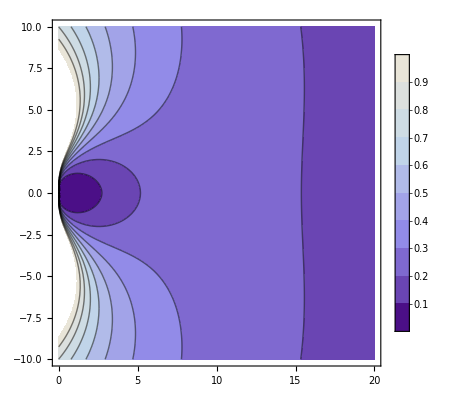

```mathematica
(* Plot convergence as function of dt*xi for k=2,4,8,16,64, with *different* RK schemes *)
butcher = GetButcher["Lob3C",4,"L",3,1];
Af=butcher[[1]];
bf=butcher[[2]];
butcherC = GetButcher["SDIRK",2,"L",2,1];
Ac=butcherC[[1]];
bc=butcherC[[2]];
Af //MatrixForm
Ac //MatrixForm
axislim = 10;
k=1;
pf=ContourPlot[phiFdiff[x+ⅈ y ,k,Af,bf,Ac,bc,1.0],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,1.0},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];Show[pf]
```

```mathematica
phiFdiff[0.025+ⅈ 0.0 ,k,Af,bf,Ac,bc,1.0]
```

0.285081

(0.416667 | -0.0833333
0.75 | 0.25)

(0.292893 | 0
0.707107 | 0.292893)

{1.98359,0.979443}

Part::partw: Part 3 of {1.81439,0.97966} does not exist.

Part::partw: Part 3 of {1.79975,0.979747} does not exist.

Part::partw: Part 3 of {1.78656,0.979831} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

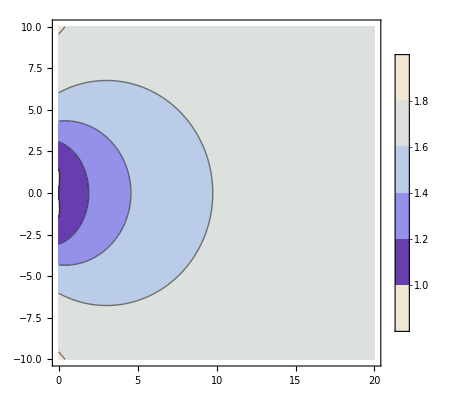

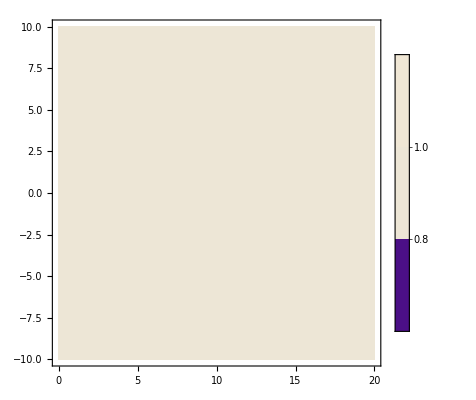

-Graphics-

```mathematica
(* Plot preconditioning of stage matrix \Phi for one RK scheme with a different.
This is *not* MGRIT convergence. *)
butcher = GetButcher["Radau",3,"A",3,1];
Af=butcher[[1]];
bf=butcher[[2]];
butcherC = GetButcher["SDIRK",2,"L",3,1];
Ac=butcherC[[1]];
(*Ac= {{Af[[1,1]],0,0},{Af[[2,1]],Af[[2,2]],0},{Af[[3,1]],Af[[3,2]],Af[[3,3]]}};*)
bc=butcherC[[2]];
Af //MatrixForm
Ac //MatrixForm
Eigenvalues[Inverse[Ac].Af]
axislim = 10;
zlim = 2.0;
pf1=ContourPlot[prec[x+ⅈ y ,Af,Ac][[1]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
pf2=ContourPlot[prec[x+ⅈ y ,Af,Ac][[2]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
pf3=ContourPlot[prec[x+ⅈ y ,Af,Ac][[3]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
Show[pf1]
Show[pf2]
Show[pf3]
```

```mathematica
butcher = GetButcher["Radau",11,"A",3,1];
A=butcher[[1]];
A //MatrixForm
Inverse[A]//MatrixForm
Eigenvalues[Inverse[A]]
```

(0.05095 | -0.0189073 | 0.0136861 | -0.01037 | 0.00736066 | -0.00290954
0.108222 | 0.106976 | -0.027539 | 0.0174967 | -0.0116537 | 0.00451224
0.0977797 | 0.223172 | 0.136315 | -0.029647 | 0.0163586 | -0.0060034
0.102122 | 0.202976 | 0.276399 | 0.131006 | -0.0248763 | 0.00783708
0.100331 | 0.210247 | 0.256085 | 0.253366 | 0.0924305 | -0.0109952
0.100794 | 0.208451 | 0.260463 | 0.242694 | 0.15982 | 0.0277778)

(12.5597 | 4.07583 | -1.2172 | 0.566232 | -0.307104 | 0.109086
-9.80284 | 2.52508 | 3.13223 | -1.15741 | 0.583382 | -0.202548
5.18216 | -5.54452 | 1.14162 | 2.97498 | -1.17802 | 0.384542
-4.10824 | 3.4915 | -5.06988 | 0.718944 | 3.46004 | -0.926443
4.38579 | -3.46401 | 3.95154 | -6.81054 | 0.554653 | 4.01713
-9.94298 | 7.67606 | -8.23274 | 11.6387 | -25.6391 | 18.5)

{4.03885+8.3456 ⅈ,4.03885-8.3456 ⅈ,6.47051+4.90012 ⅈ,6.47051-4.90012 ⅈ,7.49064+1.6215 ⅈ,7.49064-1.6215 ⅈ}

```mathematica
(8.35/4.03)^2
```

4.29302

```mathematica
AR[4]//MatrixForm
```

(0.112999 | -0.0403092 | 0.0258024 | -0.00990468
0.234384 | 0.206893 | -0.0478571 | 0.0160474
0.216682 | 0.406123 | 0.189037 | -0.0241821
0.220462 | 0.388193 | 0.328844 | 0.0625)

```mathematica
test=AR[4]
```

{{0.112999,-0.0403092,0.0258024,-0.00990468},{0.234384,0.206893,-0.0478571,0.0160474},{0.216682,0.406123,0.189037,-0.0241821},{0.220462,0.388193,0.328844,0.0625}}

```mathematica
b0 = b4[test[[4,1]],test[[4,2]],test[[4,3]],test[[4,4]]]
```

{{0.220462,0.388193,0.328844,0.0625}}

```mathematica
(* Determinants and adjugates *)
ResourceFunction["Adjugate"]
M2 = {{m11-x,m12},{m21,m22-y}};
A2 = {{m11,m12},{m21,m22}};
M3 = {{m11-xx,m12,m13},{m21,m22-yy,m23},{m31,m32,m33-zz}};
A3 = {{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}};
M4 = {{m11-xx,m12,m13,m14},{m21,m22-yy,m23,m24},{m31,m32,m33-zz,m44},{m41,m42,m43,m44-qq}};
A4 = {{m11,m12,m13,m14},{m21,m22,m23,m24},{m31,m32,m33,m44},{m41,m42,m43,m44}};
Simplify[{{"[◼]", "Adjugate"}}[Inverse[A3]].{{"[◼]", "Adjugate"}}[M3]]
```

[◼] | Adjugate

{{(m12 m23 m31-m11 m23 m32+m13 (-m22 m31+m21 m32+m31 yy)+m11 (m22-yy) (m33-zz)+m12 m21 (-m33+zz))/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33),(xx (m13 m32+m12 (-m33+zz)))/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33),(xx (m12 m23+m13 (-m22+yy)))/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33)},{(yy (m23 m31+m21 (-m33+zz)))/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33),(m13 (-m22 m31+m21 m32)+m12 (m23 m31-m21 m33+m21 zz)-(m11-xx) (m23 m32-m22 m33+m22 zz))/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33),((m13 m21+m23 (-m11+xx)) yy)/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33)},{((-m22 m31+m21 m32+m31 yy) zz)/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33),((m12 m31+m32 (-m11+xx)) zz)/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33),(m12 (m23 m31-m21 m33)+m13 (-m22 m31+m21 m32+m31 yy)-(m11-xx) (m23 m32-m22 m33+m33 yy))/(-m13 m22 m31+m12 m23 m31+m13 m21 m32-m11 m23 m32-m12 m21 m33+m11 m22 m33)}}

```mathematica
butcher = GetButcher["Radau",7,"A",3,1];
A=butcher[[1]];
A //MatrixForm
comm[M_,i_,j_,k_,l_] := M[[i,j]]*M[[k,l]] - M[[k,j]]*M[[i,l]];
comm[A,1,2,2,3]
```

(0.112999 | -0.0403092 | 0.0258024 | -0.00990468
0.234384 | 0.206893 | -0.0478571 | 0.0160474
0.216682 | 0.406123 | 0.189037 | -0.0241821
0.220462 | 0.388193 | 0.328844 | 0.0625)

-0.00340924